# Graph diameter for ICMs

## Supplementary material for Fischer et al "The salt-and-pepper pattern in mouse blastocysts is compatible with signalling beyond the nearest neighbours."

## Initialisation

```mathematica
<<(FileNameJoin[{NotebookDirectory[],"CellNucleiSegmentation_v8.m"}]) (*code from Schmitz et al. Scientific Reports 2017*)
```

```mathematica
<<(FileNameJoin[{NotebookDirectory[],"neighbourAnaFunctions_v2.m"}])(*code from Fischer et al. PLOS One 2020 and extensions*)
```

```mathematica
fontOption="Arial";
```

```mathematica
colour3[i_]:=Join[{Darker[Gray]},(ColorData[16]/@{3,6,4})][[i]]
```

```mathematica
plotMeanStdLighter[xValues_,yValues_,smooth_,xLabel_,yLabel_,colour_]:=
Show[Table[ListLinePlot[{Transpose[{xValues[[i]],MeanFilter[#[[All,1]]+#[[All,2]],smooth]}],
Transpose[{xValues[[i]],MeanFilter[#[[All,1]]-#[[All,2]],smooth]}]}&@yValues[[i]],PlotRange->{0,All},
PlotStyle->{Directive[Opacity[0.5],Lighter[colour[i],0.7]],Directive[Opacity[0.5],Lighter[colour[i],0.7]]},Filling->1->{2},FillingStyle->Directive[Opacity[0.5],Lighter[colour[i],0.5]],Frame->{True,True,None,None},FrameStyle->Directive[Black,(*Thick,*)FontFamily->fontOption,14],(*TicksStyle->Thick,*)FrameLabel->{xLabel,yLabel}],{i,1,Length[xValues]}],
ListLinePlot[Table[Transpose[{xValues[[i]],MeanFilter[#[[All,1]],smooth]}]&@yValues[[i]],{i,1,Length[xValues]}],
PlotRange->{0,All},PlotStyle->Transpose[{ConstantArray[Thickness[0.007],Length[xValues]],Table[colour[i],{i,1,Length[xValues]}]}],Frame->{True,True,None,None},FrameStyle->Directive[Black,FontFamily->fontOption,14],FrameLabel->{xLabel,yLabel}]]
```

```mathematica
populationsColours={Lighter[Orange,0.7],Gray,Darker[Purple],Darker[Green,0.7]};
```

## Graph diameter of ICM

```mathematica
allFolders={"SMD_2020_NG6","SMD_2021_NG6G4","JLG_2021_NG6","NS_2016_NG6","NS_2020_NG6","NS_2020_NRatG6Rb","NS_2020_NRatG6Gt"};
```

```mathematica
finalFNames=Flatten[FileNames["*FinalData.mx",FileNameJoin[{StringReplace[NotebookDirectory[],"analysisCode"->("dataPreProcessing\\"<>#)],"EmbryoFeatures"}]]&/@allFolders];
```

```mathematica
Length[finalFNames]
```

738

this also includes embryos at stage 3.0 which will be discarded below

```mathematica
data=Import[#]&/@finalFNames;
```

```mathematica
data[[1]]//Keys
```

{NucleiFeatures,GlobalFeatures,Staging}

```mathematica
staging=("Staging"/.data);
```

```mathematica
nucleiFeatures=("NucleiFeatures"/.data);
```

```mathematica
nucleiFeaturesICM=Table[Select[nucleiFeatures[[i]],("TE/ICM"/.#)!="TE"&],{i,1,Length[nucleiFeatures]}];
```

```mathematica
dcgGraphs=Transpose[{staging,("DelaunayCellGraph"/.("GlobalFeatures"/.data))}];
```

```mathematica
dcgGraphsICM=Table[{dcgGraphs[[i,1]],Subgraph[dcgGraphs[[i,2]],"Centroid"/.nucleiFeaturesICM[[i]]]},{i,1,Length[dcgGraphs]}];
```

the graph edges are weighted by the Euclidean distance between the respective vertices (Alex code)

```mathematica
dcgGraphsICMUnWeighted={#[[1]],Graph[el=EdgeList[#[[2]]], EdgeWeight->ConstantArray[1,Length[el]]]}&/@dcgGraphsICM;
```

```mathematica
graphDiam={#[[1]],GraphDiameter[SortBy[ConnectedGraphComponents[#[[2]]],VertexCount[#]&][[-1]]]}&/@dcgGraphsICMUnWeighted;
```

```mathematica
pos=Position[dcgGraphsICM,{"Batch3","embryoM",4.5}]
```

{{7,1}}

```mathematica
Graphics3D[{Gray,Tube[{#[[1]],#[[2]]}]&/@EdgeList[dcgGraphsICM[[pos[[1,1]],2]]],Sphere[#,6]&/@("Centroid"/.nucleiFeaturesICM[[pos[[1,1]]]])},Lighting->"Neutral",Boxed->False]
```

-Graphics3D-

```mathematica
pos=Position[dcgGraphsICM,{"Batch3","embryoV",4.5}]
```

{{16,1}}

```mathematica
Graphics3D[{Gray,Tube[{#[[1]],#[[2]]}]&/@EdgeList[dcgGraphsICM[[pos[[1,1]],2]]],Sphere[#,6]&/@("Centroid"/.nucleiFeaturesICM[[pos[[1,1]]]])},Lighting->"Neutral",Boxed->False]
```

-Graphics3D-

```mathematica
pos=Position[dcgGraphsICM,{"10 Young","10YNDembr9.ome",3.5}]
```

{{170,1}}

```mathematica
Graphics3D[{Gray,Tube[{#[[1]],#[[2]]}]&/@EdgeList[dcgGraphsICM[[pos[[1,1]],2]]],Sphere[#,6]&/@("Centroid"/.nucleiFeaturesICM[[pos[[1,1]]]])},Lighting->"Neutral",Boxed->False]
```

-Graphics3D-

```mathematica
graphDiamByStage=Table[Select[graphDiam,#[[1,3]]==i&],{i,{3.5,4.0,4.5}}];
```

```mathematica
plotDataAbs=SortBy[Tally[#[[All,2]]],#[[1]]&]&/@graphDiamByStage
```

{{{2.,5},{3.,139},{4.,175},{5.,7}},{{3.,68},{4.,141},{5.,9}},{{3.,4},{4.,94},{5.,65},{6.,12},{7.,1},{8.,1}}}

fill missing values to get the same x-axis in BarChart

```mathematica
plotDataAbsFilled=Table[Count[graphDiamByStage[[i,All,2]],#]&/@Range[2.,8.],{i,1,3}]
```

{{5,139,175,7,0,0,0},{0,68,141,9,0,0,0},{0,4,94,65,12,1,1}}

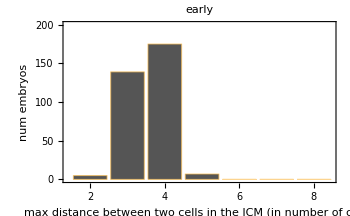
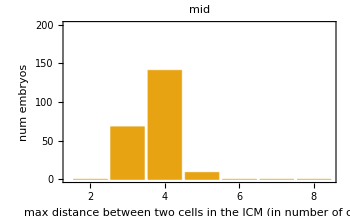
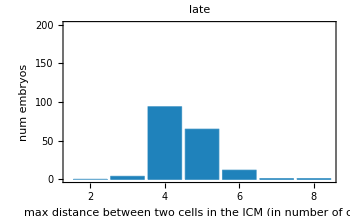

```mathematica
graphDiamPlot=Row[Table[BarChart[plotDataAbsFilled[[i]],PlotRange->{0,200},PlotLabel->Style[#,Black,20]&@({"early","mid","late"}[[i]]),ImageSize->350,ImagePadding->{{59,25},{110,5}},Frame->True,FrameLabel-> {"max distance between\ntwo cells in the ICM\n(in number of cells)","num embryos"},FrameStyle->Directive[Black,20],ChartLabels->(IntegerPart/@Range[2.,8.]),ChartStyle->(colour3[#]&@({1,2,3}[[i]]))],{i,1,3}]]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Figures","graphDiamPlotByStage.png"}],graphDiamPlot]
```